# Analisi della risposta libera (caso TC), autovalori multipli

```mathematica
ClearAll["Global`*"]
```

```mathematica
A={{-4,-2,2,-4},{-1,-3,1,-4},{-1,-1,-1,-2},{1,1,-1,1}}
```

{{-4,-2,2,-4},{-1,-3,1,-4},{-1,-1,-1,-2},{1,1,-1,1}}

Determiniamo lo spettro di A

```mathematica
λ=Eigenvalues[A]
```

{-2,-2,-2,-1}

Posso servirmi del polinomio minimo per capire se la matrice e’ diagonalizzabile o meno

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
Factor[MatrixMinimalPolynomial[A,x]]
```

(1+x) (2+x)^2

```mathematica
Factor[CharacteristicPolynomial[A,x]]
```

(1+x) (2+x)^3

Poiche’ nel polinomio minimo (x+2), legato all’autovalore multiplo non ha “esponente” unitario, deduco che la matrice NON E’ diagonalizzabile. Devo quindi ricorrere alla forma di Jordan

```mathematica
{T,Λ}=JordanDecomposition[A]
```

{{{1,2,-3,0},{0,-1,0,-2},{1,1,0,0},{0,0,1,1}},{{-2,0,0,0},{0,-2,1,0},{0,0,-2,0},{0,0,0,-1}}}

```mathematica
Λ//MatrixForm
```

(-2 | 0 | 0 | 0
0 | -2 | 1 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -1)

Per “vedere” i modi naturali, mi conviene calcolare l’esponenziale di matrice della forma canonica di Jordan di A

```mathematica
Simplify[MatrixExp[Λ t]]//MatrixForm
```

(ⅇ^(-2 t) | 0 | 0 | 0
0 | ⅇ^(-2 t) | ⅇ^(-2 t) t | 0
0 | 0 | ⅇ^(-2 t) | 0
0 | 0 | 0 | ⅇ^-t)

Analizziamo il grafico del modo polinomial-esponenziale

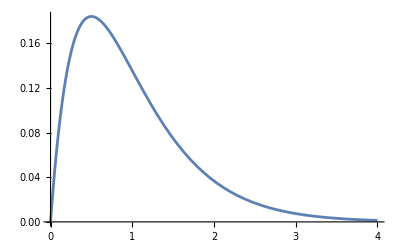

```mathematica
Plot[t Exp[-2 t],{t,0,4},PlotRange->All]
```

```mathematica
Λ//MatrixForm
```

(-2 | 0 | 0 | 0
0 | -2 | 1 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -1)

```mathematica
T//MatrixForm
```

(1 | 2 | -3 | 0
0 | -1 | 0 | -2
1 | 1 | 0 | 0
0 | 0 | 1 | 1)

Mi calcolo la risposta libera (inserisco x0)

```mathematica
Subscript[x, 0]={{1},{1},{0},{0}}
```

{{1},{1},{0},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{5},{-5},{-2},{2}}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

RIsposta libera nell’uscita

```mathematica
C1={0,1,0,0}
```

{0,1,0,0}

```mathematica
Subscript[y, l][t_]:=C1.Subscript[x, l][t]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-5 ⅇ^(-2 t)-2 (-3 ⅇ^(-2 t)+2 ⅇ^(-2 t) t)
5 ⅇ^(-2 t)-4 ⅇ^-t+2 ⅇ^(-2 t) t
-2 ⅇ^(-2 t) t
-2 ⅇ^(-2 t)+2 ⅇ^-t)

```mathematica
Subscript[y, l][t]
```

{5 ⅇ^(-2 t)-4 ⅇ^-t+2 ⅇ^(-2 t) t}

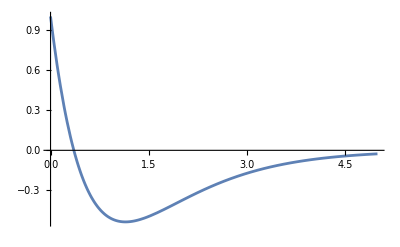

```mathematica
Plot[Subscript[y, l][t],{t,0,5},PlotRange->All]
```

```mathematica
T//MatrixForm
```

(1 | 2 | -3 | 0
0 | -1 | 0 | -2
1 | 1 | 0 | 0
0 | 0 | 1 | 1)

```mathematica
MatrixExp[Λ t]//MatrixForm
```

(ⅇ^(-2 t) | 0 | 0 | 0
0 | ⅇ^(-2 t) | ⅇ^(-2 t) t | 0
0 | 0 | ⅇ^(-2 t) | 0
0 | 0 | 0 | ⅇ^-t)

```mathematica
Subscript[x, 0]={{2},{-1},{1},{0}}
```

{{2},{-1},{1},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{1},{0},{0}}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(2 ⅇ^(-2 t)
-ⅇ^(-2 t)
ⅇ^(-2 t)
0)

```mathematica
Subscript[x, 0]={{1},{0},{1},{0}}
```

{{1},{0},{1},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{1},{0},{0},{0}}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(ⅇ^(-2 t)
0
ⅇ^(-2 t)
0)

```mathematica
Subscript[x, 0]={{-3},{0},{0},{1}}
```

{{-3},{0},{0},{1}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{0},{1},{0}}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-3 ⅇ^(-2 t)+2 ⅇ^(-2 t) t
-ⅇ^(-2 t) t
ⅇ^(-2 t) t
ⅇ^(-2 t))

“Cambio” il sistema

```mathematica
ClearAll["Global`*"]
```

```mathematica
A={{2,1,-4,-4},{22,7,-25,-28},{12,5,-15,-14},{-1,-1,1,-1}}
```

{{2,1,-4,-4},{22,7,-25,-28},{12,5,-15,-14},{-1,-1,1,-1}}

Calcolo lo spettro

```mathematica
λ=Eigenvalues[A]
```

{-2,-2,-2,-1}

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

Test del polinomio minimo per capire se la matrice e’ diagonalizzabile o meno

```mathematica
Factor[MatrixMinimalPolynomial[A,x]]
```

(1+x) (2+x)^3

```mathematica
Factor[CharacteristicPolynomial[A,x]]
```

(1+x) (2+x)^3

La matrice non e’ diagonalizzabile e quindi devo ricorrere alla Forma di Jordan

```mathematica
{T,Λ}=JordanDecomposition[A]
```

{{{-1,-3,-5,2},{0,-1,1,-2},{-2,-3,-4,0},{1,0,0,1}},{{-2,1,0,0},{0,-2,1,0},{0,0,-2,0},{0,0,0,-1}}}

```mathematica
Λ//MatrixForm
```

(-2 | 1 | 0 | 0
0 | -2 | 1 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -1)

```mathematica
T//MatrixForm
```

(-1 | -3 | -5 | 2
0 | -1 | 1 | -2
-2 | -3 | -4 | 0
1 | 0 | 0 | 1)

Per “vedere” i modi mi calcolo l’esponenziale di Matrice della forma canonica

```mathematica
MatrixExp[Λ t]//MatrixForm
```

(ⅇ^(-2 t) | ⅇ^(-2 t) t | 1/2 ⅇ^(-2 t) t^2 | 0
0 | ⅇ^(-2 t) | ⅇ^(-2 t) t | 0
0 | 0 | ⅇ^(-2 t) | 0
0 | 0 | 0 | ⅇ^-t)

Analisi del grafico del modo polinomial-esponenziale con polinomio “parabolico”

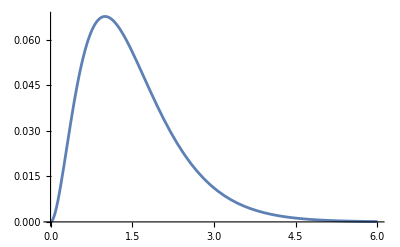

```mathematica
Plot[1/2 ⅇ^(-2 t) t^2,{t,0,6},PlotRange->All]
```

```mathematica
T//MatrixForm
```

(-1 | -3 | -5 | 2
0 | -1 | 1 | -2
-2 | -3 | -4 | 0
1 | 0 | 0 | 1)

Calcoliamo ora la risposta libera “senza preoccuparci” di direzioni privilegiate (colonne di T)

```mathematica
Subscript[x, 0]={{1},{0},{1},{0}}
```

{{1},{0},{1},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{-1},{-1},{1},{1}}

```mathematica
C1={2,0,1,0}
```

{2,0,1,0}

```mathematica
T//MatrixForm
```

(-1 | -3 | -5 | 2
0 | -1 | 1 | -2
-2 | -3 | -4 | 0
1 | 0 | 0 | 1)

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[y, l][t_]:=Simplify[C1.Subscript[x, l][t]]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-ⅇ^(-2 t)+2 ⅇ^-t-2 ⅇ^(-2 t) t-1/2 ⅇ^(-2 t) t^2
2 ⅇ^(-2 t)-2 ⅇ^-t-ⅇ^(-2 t) t
ⅇ^(-2 t)-ⅇ^(-2 t) t-ⅇ^(-2 t) t^2
-ⅇ^(-2 t)+ⅇ^-t-ⅇ^(-2 t) t+1/2 ⅇ^(-2 t) t^2)

```mathematica
Expand[Subscript[y, l][t]]
```

{-ⅇ^(-2 t)+4 ⅇ^-t-5 ⅇ^(-2 t) t-2 ⅇ^(-2 t) t^2}

```mathematica
MatrixExp[Λ t]//MatrixForm
```

(ⅇ^(-2 t) | ⅇ^(-2 t) t | 1/2 ⅇ^(-2 t) t^2 | 0
0 | ⅇ^(-2 t) | ⅇ^(-2 t) t | 0
0 | 0 | ⅇ^(-2 t) | 0
0 | 0 | 0 | ⅇ^-t)

```mathematica
T//MatrixForm
```

(-1 | -3 | -5 | 2
0 | -1 | 1 | -2
-2 | -3 | -4 | 0
1 | 0 | 0 | 1)

```mathematica
Subscript[x, 0]={{2},{-2},{0},{1}}
```

{{2},{-2},{0},{1}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{0},{0},{1}}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(2 ⅇ^-t
-2 ⅇ^-t
0
ⅇ^-t)

```mathematica
Subscript[x, 0]=Transpose[T[[All,1]]]
```

{-1,0,-2,1}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{1,0,0,0}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-ⅇ^(-2 t)
0
-2 ⅇ^(-2 t)
ⅇ^(-2 t))

```mathematica
Subscript[x, 0]
```

{-1,0,-2,1}

```mathematica
Subscript[x, 0]=Transpose[T[[All,2]]]
```

{-3,-1,-3,0}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{0,1,0,0}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-3 ⅇ^(-2 t)-ⅇ^(-2 t) t
-ⅇ^(-2 t)
-3 ⅇ^(-2 t)-2 ⅇ^(-2 t) t
ⅇ^(-2 t) t)

```mathematica
Subscript[x, 0]=Transpose[T[[All,3]]]
```

{-5,1,-4,0}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{0,0,1,0}

```mathematica
Subscript[x, l][t_]:=T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-5 ⅇ^(-2 t)-3 ⅇ^(-2 t) t-1/2 ⅇ^(-2 t) t^2
ⅇ^(-2 t)-ⅇ^(-2 t) t
-4 ⅇ^(-2 t)-3 ⅇ^(-2 t) t-ⅇ^(-2 t) t^2
1/2 ⅇ^(-2 t) t^2)